## Solutions: Mathematica 6 Lab 2

Problem 1:

Nick: The PlotPoints stuff is now irrelevant.  Rotate, see how nicely the mesh responds.

```mathematica
Plot3D[Sin[π Sin[x]+y],{x,-3,3},{y,-3,3},Boxed->False,Axes->None,Mesh->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[π Sin[x]+y],{x,-3,3},{y,-3,3},Boxed->False,Axes->None,Mesh->40]
```

-Graphics3D-

Problem 2:

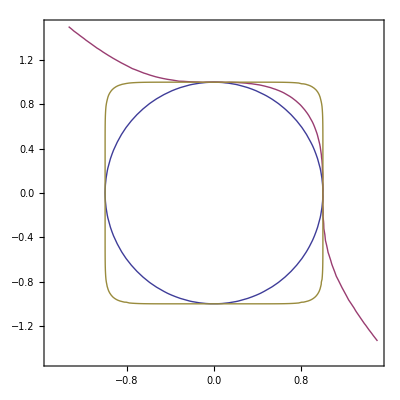

```mathematica
ContourPlot[{x^2+y^2==1,x^3+y^3==1,x^10+y^10==1},{x,-1.5,1.5}, {y,-1.5,1.5}]
```

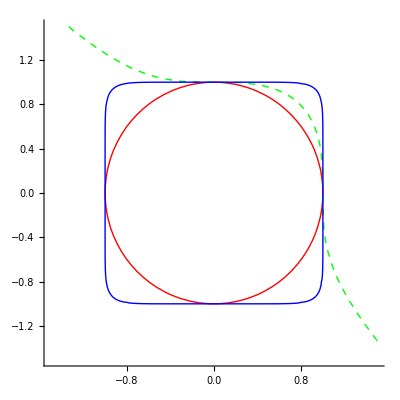

```mathematica
ContourPlot[{x^2+y^2==1,x^3+y^3==1,x^10+y^10==1},{x,-1.5,1.5}, {y,-1.5,1.5},ContourStyle->{{Red,Thick},{Green,Thick, Dashed},{Blue,Thick}},Axes->True , Frame->False]
```

Problem 3:

```mathematica
Plot3D[ⅇ^(-x^8-y^8),{x,-2,2},{y,-2,2}, Ticks->False, Mesh->25]
```

-Graphics3D-

```mathematica
Plot3D[ⅇ^(-x^8-y^8),{x,-2,2},{y,-2,2}, Ticks->False, Mesh->25, PlotPoints->50]
```

-Graphics3D-

Problem 4:

```mathematica
g=ParametricPlot3D[{r Cos[t],r Sin[t], Cos[t]Sin[t]},{r,0,1},{t,0,2π}, Boxed->False,Axes->False]
```

-Graphics3D-

Problem 5:

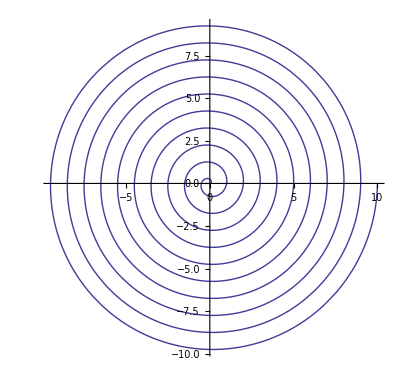

```mathematica
ParametricPlot[{s Cos[2 π s+0],s Sin[2 π s+0]},{s,0,10}]
```

```mathematica
Manipulate[ParametricPlot[{s Cos[2 π s+t],s Sin[2 π s+t]},{s,0,10}, PlotRange->{{-10,10},{-10,10}}],{t,0,2π}]
```